Algorithm:by code developed python myself.Null

100

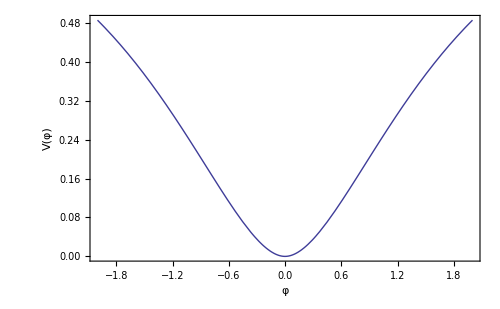

10

20

30

40

50

60

70

80

90

100

{507.46875,Null}

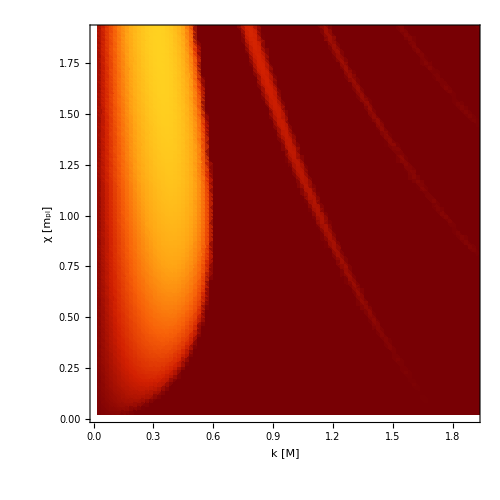

-Graphics3D-

```mathematica
(*The code is performing a numerical analysis of a system described by a differential equation,which represents a physical system with a potential V.The potential is defined as a piecewise function,and the system is analyzed for a range of initial conditions and wave numbers.The system's behavior is characterized by a quantity called the Floquet exponent,which is computed for each set of conditions.The Floquet exponent is a concept from the theory of differential equations,and it describes the stability of periodic solutions to those equations.In this case,the differential equation is a second-order equation (it involves the second derivative of a function),which is typical of systems in classical mechanics.The code then generates a 3D plot of the Floquet exponent as a function of the wave number and the initial condition.Here's a simplified explanation of each part of the code:Variable and function definitions:The code begins by clearing any previous definitions of the variables and functions that will be used.It then defines the potential V and the initial conditions for the field and wave number.Plotting the potential:The potential V is plotted as a function of the field.Main loop:The main part of the code is a nested loop that iterates over the range of initial conditions and wave numbers.For each combination,it computes the period of oscillation of the system,solves the differential equation for two fundamental solutions,computes the Floquet exponent,and stores the result.Data collection and visualization:The results are collected into a list and then visualized using a density plot and a 3D plot.*)


(*The program uses the equations of motion for the field and its fluctuations and applies Floquet theory to find solutions.The Floquet exponent,denoted as Subscript[[Mu],k],measures the exponential growth of solutions and depends on the field amplitude ([CurlyPhi]) and the wavenumber of the fluctuations (k).Positive values of Re[Subscript[[Mu],k]] indicate unstable solutions.The algorithm used by FloqEx involves several steps:Determine the period of the field ([CurlyPhi]) based on the given potential function.Solve the equation of motion for the field with appropriate initial conditions.Solve the equation of motion for the fluctuations using two sets of initial conditions derived from the solution obtained in step 2.
Construct the Monodromy matrix,which describes the evolution of solutions over one period.Find the eigenvalues of the Monodromy matrix.Calculate the Floquet exponent using the eigenvalues,determining the stability of the system.The output of the program is a table of values representing the Floquet exponent for different combinations of k and[CurlyPhi].These values can be used to create contour plots,where regions with positive values of Re[Subscript[[Mu],k]] correspond to unstable solutions.The program provides options to specify the potential function,grid spacing,and the range of values for[CurlyPhi] and k.*)
Algorithm:(*Here is how my algorithm works for a given k andSubscript[φ, 0].The grid is populated by repeating this step.

 Obtain the periodT(Subscript[φ, 0]) =2×(∫_Subscript[φ, m])^Subscript[φ, 0] dφ/(√(2V(Subscript[φ, 0])-2V(φ)))(whereV(Subscript[φ, m])=V(Subscript[φ, 0]))
2) Solveφ^(..)+V'(φ)=0with the initial conditionsφ(Subscript[t, 0])=Subscript[φ, 0]andφ̇(Subscript[t, 0])=0uptoT(Subscript[φ, 0])
3) Using the solutionφ(t)from (1),solveSubscript[δφ, k]^(..)+(k^2+V''(φ))Subscript[δφ, k]=0for two sets of initial conditions initial conditions
Π(Subscript[t, 0])=({{Subscript[δφ^(1), k](Subscript[t, 0]), Subscript[δφ^(2), k](Subscript[t, 0])}, {Subscript[OverDot[δφ]^(1), k](Subscript[t, 0]), Subscript[OverDot[δφ]^(2), k](Subscript[t, 0])}})=({{1, 0}, {0, 1}})
4) Using (3),construct theMonodromymatrixM(Subscript[t, 0])=Π(Subscript[t, 0]+T)M=({{Subscript[δφ^(1), k](T), Subscript[δφ^(2), k](T)}, {Subscript[OverDot[δφ]^(1), k](T), Subscript[OverDot[δφ]^(2), k](T)}})and find it's eigenvaluesSubscript[m, 1]=e^(Subscript[μ, 1] T)andSubscript[m, 2]=e^(Subscript[μ, 2] T)(called the Floquet multipliers).6) We have an unstable solution,Re[Subscript[μ, k]]>0iff|m|>1.The Floquet exponent of interest to us is



Subscript[μ, k]=1/T ln m    wherem=max{|Subscript[m, 1]|,|Subscript[m, 2]|,1}
a) runtime~((# of grid points)/2000) 1 min.Usually it is a lot faster.
b) If you see jagged structures,it usually means Δk and Δφ should be reduced..*)
python code developed by myself.
(*
for the equation 
floquetRHS1[t_,A0_,dA0_,k_,mgammaPrime_,phi0_,mphi_,M_]:=Module[{phiBar,d2A0},phiBar=phi0*Cos[mphi*t];
d2A0=-(k^2+(mgammaPrime^2)/Exp[phiBar/M])*A0;
{dA0,d2A0}];

floquetRHS2[t_,A0_,dA0_,k_,mgammaPrime_,phi0_,mphi_,M_]:=Module[{phiBar,dphiBar,ddphiBar,d2A0},phiBar=phi0*Cos[mphi*t];
dphiBar=-phi0*mphi*Sin[mphi*t];
ddphiBar=-phi0*mphi^2*Cos[mphi*t];
d2A0=-(k^2+(mgammaPrime^2)/Exp[phiBar/M]-(ddphiBar/(2*M))-(dphiBar/(2*M))^2)*A0;
{dA0,d2A0}];
from here the code starts .
import numpy as np
import matplotlib.pyplot as plt
import cmasher as cmr
from scipy.integrate import solve_ivp

m_phi=1.0
M=1.0

def dilaton(t):return phi_0*np.cos(m_phi*t)

def dilaton_derivative(t):return-phi_0*m_phi*np.sin(m_phi*t)

def dilaton_double_derivative(t):return-phi_0*m_phi**2*np.cos(m_phi*t)

def floquet_rhs_1(t,X,k,m_gamma_prime):A0,dA0=X
phi_bar=dilaton(t)

d2A0=-(k**2+(m_gamma_prime**2)/np.exp(phi_bar/M))*A0

return[dA0,d2A0]

def floquet_rhs_2(t,X,k,m_gamma_prime):A0,dA0=X
phi_bar=dilaton(t)
dphi_bar=dilaton_derivative(t)
ddphi_bar=dilaton_double_derivative(t)

d2A0=-(k**2+(m_gamma_prime**2)/np.exp(phi_bar/M)-(ddphi_bar/(2*M))-(dphi_bar/(2*M))**2)*A0

return[dA0,d2A0]

phi0_values=np.linspace(0.01,6,530)
k_values=np.linspace(0.01,3,530)

Re_mu_grid_1=np.zeros((len(phi0_values),len(k_values)))
Re_mu_grid_2=np.zeros((len(phi0_values),len(k_values)))

m_gamma_prime=0.5*m_phi

T=2*np.pi/m_phi
t_eval=np.linspace(0,10*T,1000)

for i,phi_0 in enumerate(phi0_values):for j,k in enumerate(k_values):initial_conditions=[1.0,0.0]

sol_1=solve_ivp(floquet_rhs_1,(0,10*T),initial_conditions,args=(k,m_gamma_prime),t_eval=t_eval,method='RK45')
final_A0_1=sol_1.y[0][-1]
Re_mu_1=(1/(10*T))*np.log(np.abs(final_A0_1/initial_conditions[0]))
Re_mu_1=np.maximum(0,Re_mu_1)
Re_mu_grid_1[i,j]=Re_mu_1

sol_2=solve_ivp(floquet_rhs_2,(0,10*T),initial_conditions,args=(k,m_gamma_prime),t_eval=t_eval,method='RK45')
final_A0_2=sol_2.y[0][-1]
Re_mu_2=(1/(10*T))*np.log(np.abs(final_A0_2/initial_conditions[0]))
Re_mu_2=np.maximum(0,Re_mu_2)
Re_mu_grid_2[i,j]=Re_mu_2

k_grid,phi0_grid=np.meshgrid(k_values/m_phi,phi0_values/M)

fig,axs=plt.subplots(1,2,figsize=(12,6))

cs1=axs[0].contourf(k_grid,phi0_grid,Re_mu_grid_1,levels=100,cmap=cmr.ocean_r)
axs[0].set_title("Real part of Floquet exponent ('$A_0$')")
axs[0].set_xlabel('$k/m_{\phi}$')
axs[0].set_ylabel('$\phi_0/M$')
cs2=axs[1].contourf(k_grid,phi0_grid,Re_mu_grid_2,levels=100,cmap=cmr.ocean_r)
axs[1].set_title("Real part of Floquet exponent ('$A_+-$')")
axs[1].set_xlabel('$k/m_{\phi}$')
axs[1].set_ylabel('$\phi_0/M$')
plt.tight_layout()
plt.show()
-Graphics-
*)
(*mathematica code modifeid and simplified by me , the core idea is taken from mustafa amin paper on floquet theory*)
Clear[Floquet,φSol,φ0,φ0m,i,j,k,δφSol,μ,imin,jmax,jmin,imax,V,α,Δφ,Δk,T,t0]
Clear[H,V,Mpl]
(*You will likely want to change things in red based on the problem*)
α=1/2; (*This the exponent in the monodromy like models*)
V[φ_]:=If[φ<0,3/4(1-E^(√(2/3)φ))^2,3/4(1-E^(-√(2/3)φ))^2](*Potential: any potential with a local minimum at 0 should be fine. Mathieu equation is recovered (approx) for α=2 *) 
Δφ=0.02;           (* field spacing *)
Δk=0.02;          (* k spacing *)
jmin=1;          (* = φmin/Δφ *)
jmax=100         (* = φmax/Δφ, make sure you don't have any additional extrema beyween 0 and φmax, else bad things will happen*)  
imin=1;            (* = kmin/Δk *)
imax=100;        (* = kmax/Δk *)


φ0[j_]:=j Δφ;(* initial amplitude of the pump field grid *)
k[i_]:=i Δk;   (* wave number grid *)
Plot[V[φ],{φ,-φ0[jmax],φ0[jmax]},Frame->True,FrameStyle->20,FrameLabel->{"φ","V(φ)",""," "},ImageSize->500,PlotStyle->Thick]
For[j=jmin,j≤jmax,j++,
t0=0.;
φ0m[j]=φ/.FindRoot[V[φ]==V[φ0[j]],{φ,-φ0[j]}];(*this is the other extremum of the oscillation, sometimes this step is problematic*)
T=2Abs[NIntegrate[1/(√(2(V[φ0[j]]-V[φ]))),{φ,φ0m[j],φ0[j]}]];(*calculate the period of oscillation *)
φSol=φ[t]/.NDSolve[{φ''[t]+V'[φ[t]]==0,φ[t0]==j Δφ,φ'[t0]==0},φ[t],{t,t0,T}][[1]];
If[Mod[j,10]==0,Print[j]];(*This just prints what step you are at*)
For[i=imin,i≤imax,i++,
δφSol1=δφ[t]/.NDSolve[{δφ''[t]+(k[i]^2+V''[φSol])δφ[t]==0,δφ[t0]==1,δφ'[t0]==0},δφ[t],{t,t0,T}][[1]];(*this is one of the two fundamental solutions*)
δφSol2=δφ[t]/.NDSolve[{δφ''[t]+(k[i]^2+V''[φSol])δφ[t]==0,δφ[t0]==0,δφ'[t0]==1},δφ[t],{t,t0,T}][[1]];
(*this is one of the two fundamental solutions*)
dδφSol1=D[δφSol1, t];
dδφSol2=D[δφSol2, t];
M=({{δφSol1, δφSol2}, {dδφSol1, dδφSol2}})/.t->T;(*Monodromy matrix*)
eigenM=Eigenvalues[M];(* floquet multipliers *)
max[i]=Max[Abs[eigenM[[1]]],Abs[eigenM[[2]]],1];(*decide whether you have a real floquet exponent, is |m|>1?*)
μ[j,i]=1/T Log[max[i]]];(* floquet exponent, the real ones *)
Clear[eigenM,max,M,δφSol1,δφSol2,dδφSol2,dδφSol1,T,φ0m]]//Timing

Floquet=Flatten[Table[{k[i],φ0[j],μ[j,i]},{i,imin,imax},{j,jmin,jmax}],1]; (*This is a table with {k,φ, Re[Subscript[μ, k]]}*)
(*3D plot. You can control the visualization as you please*)
ListDensityPlot[Floquet,PlotRange->{{imin Δk,1.9},{jmin Δφ,1.9},All},FrameStyle->20,FrameLabel->{"k [M]","χ [m_pl]",""," "},ImageSize->500,ColorFunction->ColorData["SolarColors"]](*Contour plot. You can control the output here*)
ListPlot3D[Floquet,PlotRange->All,Axes->True,AxesLabel->{"wavenumber k","pump field φ","Re[μ_k]"},ImageSize->500,BoxRatios->{1,1,0.8}]
```